```mathematica
Remove["Global`*"]
```

Numerical solution to a partial differential equation, namely the transverse vibrational motion of a stretched string, fixed at both ends, as a function of time. 
Transverse vibrations of a stretch string follows from the wave equation we where u(x,t) is the shape of the string for a longitudinal position x at time t.

Consider a string with shape u(x,0) = (L/2 - x)^2 (L/2 + x)^2 where the string extends from x = -L/2 to x = L/2 and is fixed at the endpoints so u(+-L/2,t) = 0
Find u(x,t), L = l

```mathematica
v = 2;
l = 5;
```

```mathematica
we = (1/v^2)*(D[u[x,t],{t,2}])== D[u[x,t],{x,2}];
```

```mathematica
sol = NDSolve[{we,Derivative[0,1][u][x,0]==0,u[x,0]==((l/2-x)^2 ) *((l/2+x)^2), u[-l/2,t]==0, u[l/2,t]==0},u[x,t], {x,-l/2, l/2}, {t, 0, l/v}]
```

NDSolve::eerr: Warning: scaled local spatial error estimate of 644.948 at t = 2.5 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{u[x,t]→InterpolatingFunction[…][x,t]}}

```mathematica
U = u[x,t]/.sol
```

{InterpolatingFunction[…][x,t]}

```mathematica
U0 = u[x,t]/.sol/.t->0
```

{InterpolatingFunction[…][x,0]}

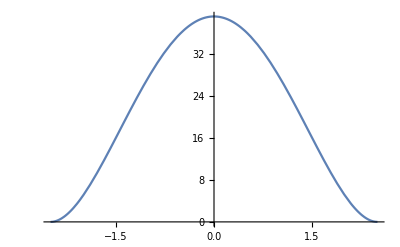

```mathematica
Plot[U0, {x,-l/2,l/2}]
```

```mathematica
Animate[Plot[u[x,t]/.sol/. t->ti, {x,-l/2,l/2}, PlotRange->{-40,40}], {ti,0, l/v}, AnimationRunning->True]
```